A < 0.25

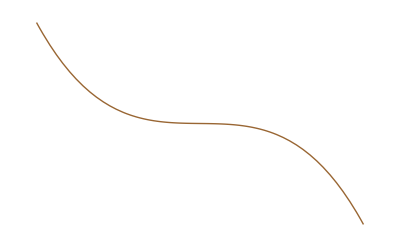

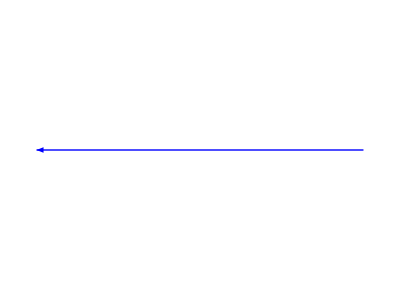

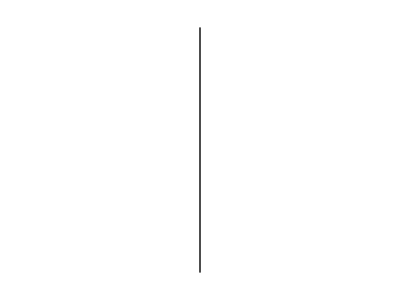

-Graphics-

-Graphics-

-Graphics-

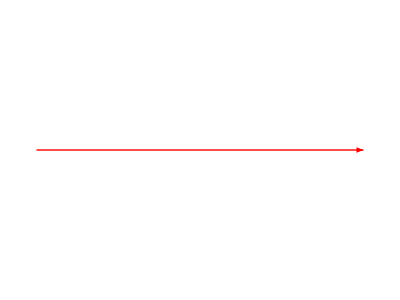

-Graphics-

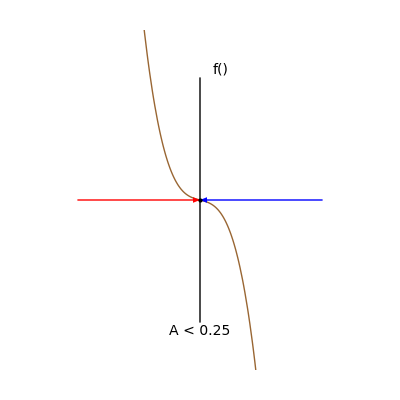

```mathematica
fxn=Plot[-0.25x - 1.5*x^3,{x,-3,3},Frame->False,Axes->False,PlotStyle->{Thick,Brown}]
left=Graphics[{Blue,Thick,Arrow[{{3,0},{-0,0}}]}]
yaxis=Graphics[Line[{{0,-3},{0,3}}]]
t1=Graphics[Text[Style["",FontSize->14,Black],{3.2,-0.5}]]
t2=Graphics[Text[Style["f()",FontSize->14,Black],{0.5,3.2}]]
t3=Graphics[Text[Style["A < 0.25",FontSize->14,Black],{0.0,-3.2}]]
right=Graphics[{Red,Thick,Arrow[{{-3,0},{0,0}}]}]
origin = Graphics[{PointSize[Large],Point[{0,0}]}]
Show[fxn,left,yaxis,t1,t2,t3,right,origin, AspectRatio->1,PlotRange->{{-4,4},{-4,4}}]
```

A = 0.25

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

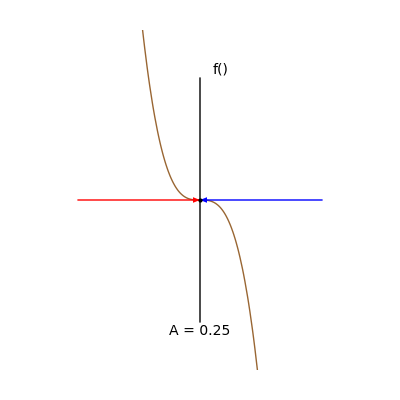

```mathematica
fxn=Plot[-1.5*x^3,{x,-3,3},Frame->False,Axes->False,PlotStyle->{Thick,Brown}]
left=Graphics[{Blue,Thick,Arrow[{{3,0},{-0,0}}]}]
yaxis=Graphics[Line[{{0,-3},{0,3}}]]
t1=Graphics[Text[Style["",FontSize->14,Black],{3.2,-0.5}]]
t2=Graphics[Text[Style["f()",FontSize->14,Black],{0.5,3.2}]]
t3=Graphics[Text[Style["A = 0.25",FontSize->14,Black],{0.0,-3.2}]]
right=Graphics[{Red,Thick,Arrow[{{-3,0},{0,0}}]}]
origin = Graphics[{PointSize[Large],Point[{0,0}]}]
Show[fxn,left,yaxis,t1,t2,t3,right,origin, AspectRatio->1,PlotRange->{{-4,4},{-4,4}}]
```

A > 0.25

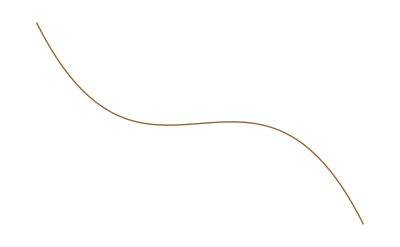

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-



-Graphics-

-Graphics-

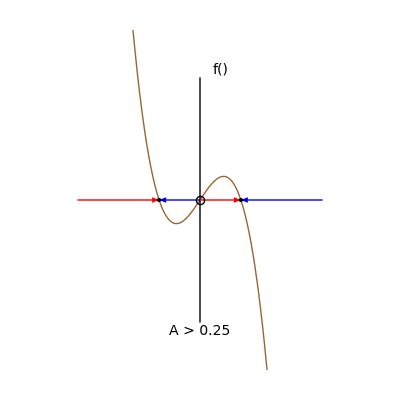

```mathematica
fxn=Plot[1.5*x-1.5*x^3,{x,-3,3},Frame->False,Axes->False,PlotStyle->{Thick,Brown}]
left1=Graphics[{Blue,Thick,Arrow[{{0,0},{-1,0}}]}]
left2 = Graphics[{Blue,Thick,Arrow[{{3,0},{1,0}}]}]
yaxis=Graphics[Line[{{0,-3},{0,3}}]]
t1=Graphics[Text[Style["",FontSize->14,Black],{3.2,-0.5}]]
t2=Graphics[Text[Style["f()",FontSize->14,Black],{0.5,3.2}]]
t3=Graphics[Text[Style["A > 0.25",FontSize->14,Black],{0.0,-3.2}]]
right1=Graphics[{Red,Thick,Arrow[{{-3,0},{-1,0}}]}]
right2 = Graphics[{Red,Thick,Arrow[{{0,0},{1,0}}]}]
origin = Graphics[Circle[{0,0},0.1],AspectRatio->1]
leftpoint = Graphics[{PointSize[Large],Point[{-1,0}]}]
rightpoint = Graphics[{PointSize[Large],Point[{1,0}]}]
Show[fxn,left1,left2, yaxis,t1,t2,t3,right1,right2, origin, leftpoint, rightpoint, AspectRatio->1,PlotRange->{{-4,4},{-4,4}}]
```

Bifurcation

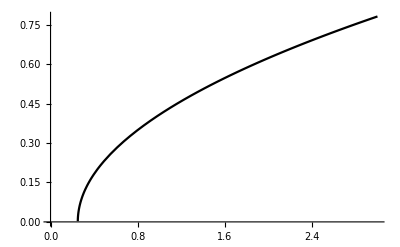

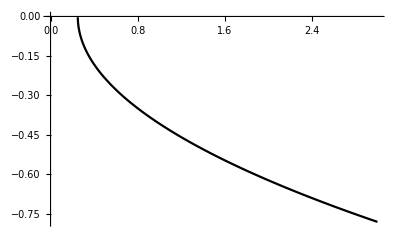

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

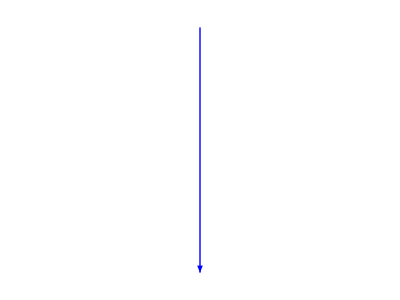

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

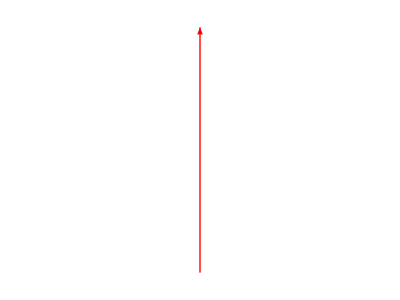

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

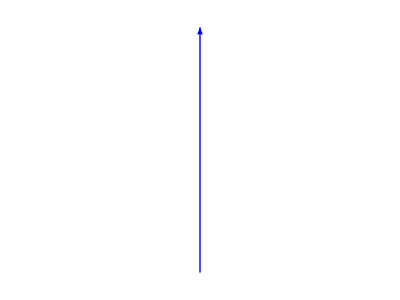

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

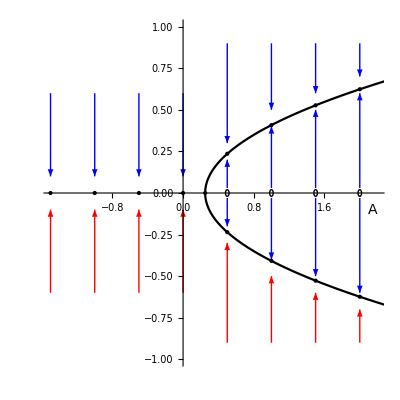

```mathematica
fxn1=Plot[Sqrt[2*(x - 0.25)]/3,{x,0,3},PlotStyle->{Medium,Black}]
fxn2 = Plot[(-Sqrt[2*(x - 0.25)]/3),{x,0,3},PlotStyle->{Medium,Black}]
s1 = Graphics[{PointSize[Medium],Point[{-1.5,0}]}]
s2 = Graphics[{PointSize[Medium],Point[{-1,0}]}]
s3 = Graphics[{PointSize[Medium],Point[{-0.5,0}]}]
s4 = Graphics[{PointSize[Medium],Point[{0,0}]}]
s5 = Graphics[{PointSize[Medium],Point[{0.25,0}]}]
us1 = Graphics[Circle[{0.5,0},0.02],AspectRatio->1]
us2 = Graphics[Circle[{1,0},0.02],AspectRatio->1]
us3 = Graphics[Circle[{1.5,0},0.02],AspectRatio->1]
us4 = Graphics[Circle[{2,0},0.02],AspectRatio->1]
p1 = Graphics[{PointSize[Medium],Point[{0.5,Sqrt[2*(0.5 - 0.25)]/3}]}]
p2 = Graphics[{PointSize[Medium],Point[{1,Sqrt[2*(1 - 0.25)]/3}]}]
p3 = Graphics[{PointSize[Medium],Point[{1.5,Sqrt[2*(1.5 - 0.25)]/3}]}]
p4 = Graphics[{PointSize[Medium],Point[{2,Sqrt[2*(2 - 0.25)]/3}]}]
p5 = Graphics[{PointSize[Medium],Point[{0.5,-Sqrt[2*(0.5 - 0.25)]/3}]}]
p6 = Graphics[{PointSize[Medium],Point[{1,-Sqrt[2*(1 - 0.25)]/3}]}]
p7 = Graphics[{PointSize[Medium],Point[{1.5,-Sqrt[2*(1.5 - 0.25)]/3}]}]
p8 = Graphics[{PointSize[Medium],Point[{2,-Sqrt[2*(2 - 0.25)]/3}]}]
b1 = Graphics[{Blue,Arrow[{{-1.5,0.6},{-1.5,0.1}}]}]
b2 = Graphics[{Blue,Arrow[{{-1,0.6},{-1,0.1}}]}]
b3 = Graphics[{Blue,Arrow[{{-0.5,0.6},{-0.5,0.1}}]}]
b4 = Graphics[{Blue,Arrow[{{0,0.6},{0,0.1}}]}]
b5 = Graphics[{Blue,Arrow[{{0.5,0.9},{0.5,0.3}}]}]
b6 = Graphics[{Blue,Arrow[{{1,0.9},{1,0.5}}]}]
b7 =Graphics[{Blue,Arrow[{{1.5,0.9},{1.5,0.6}}]}]
b8 = Graphics[{Blue,Arrow[{{2,0.9},{2,0.7}}]}]
b9 = Graphics[{Blue,Arrow[{{0.5,-0.03},{0.5,-0.2}}]}]
b10 = Graphics[{Blue,Arrow[{{1,-0.03},{1,-0.4}}]}]
b11 = Graphics[{Blue,Arrow[{{1.5,-0.03},{1.5,-0.5}}]}]
b12 = Graphics[{Blue,Arrow[{{2,-0.03},{2,-0.6}}]}]
r1 = Graphics[{Red,Arrow[{{-1.5,-0.6},{-1.5,-0.1}}]}]
r2 = Graphics[{Red,Arrow[{{-1,-0.6},{-1,-0.1}}]}]
r3 = Graphics[{Red,Arrow[{{-0.5,-0.6},{-0.5,-0.1}}]}]
r4 = Graphics[{Red,Arrow[{{0,-0.6},{0,-0.1}}]}]
r5 = Graphics[{Red,Arrow[{{0.5,-0.9},{0.5,-0.3}}]}]
r6 = Graphics[{Red,Arrow[{{1,-0.9},{1,-0.5}}]}]
r7 =Graphics[{Red,Arrow[{{1.5,-0.9},{1.5,-0.6}}]}]
r8 = Graphics[{Red,Arrow[{{2,-0.9},{2,-0.7}}]}]
r9 = Graphics[{Blue,Arrow[{{0.5,0.03},{0.5,0.2}}]}]
r10 = Graphics[{Blue,Arrow[{{1,0.03},{1,0.4}}]}]
r11 = Graphics[{Blue,Arrow[{{1.5,0.03},{1.5,0.5}}]}]
r12 = Graphics[{Blue,Arrow[{{2,0.03},{2,0.6}}]}]
t1=Graphics[Text[Style["",FontSize->14,Black],{0.2,0.95}]]
t2 = Graphics[Text[Style["A",FontSize->14,Black],{2.15,-0.1}]]
Show[fxn1,fxn2,s1, s2,s3, s4, s5, us1, us2,us3, us4, p1,p2,p3,p4,p5,p6,p7,p8, b1,b2,b3,b4,b5,b6,b7,b8,b9,b10, b11,b12,r1,r2,r3,r4,r5,r6,r7,r8,r9,r10,r11,r12,t1, t2,AspectRatio->1, PlotRange->{{-1.5,2.2},{-1,1}}]
```